```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

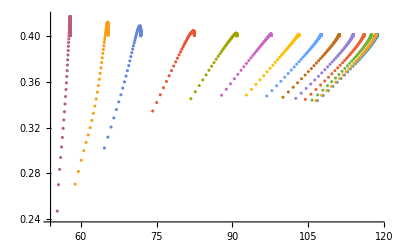

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
Table[Flatten[FindRoot[fitfun[[i]][x]-0.37==0,{x,fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p37.dat",%];
```

{113.046,112.747,111.841,110.31,108.119,105.221,101.554,97.0511,91.6519,85.3096,77.9437,69.2092,63.8864,57.2727}

```mathematica
Table[Flatten[FindRoot[fitfun[[i]][x]-0.36==0,{x,fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p36.dat",%];
```

{110.784,110.486,109.586,108.067,105.898,103.041,99.4481,95.0755,89.8899,83.8598,76.8837,68.6151,63.5595,57.1403}

```mathematica
Table[Flatten[FindRoot[fitfun[[i]][x]-0.38==0,{x,fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p38.dat",%];
```

{115.174,114.874,113.969,112.438,110.241,107.325,103.615,99.0193,93.441,86.8013,79.0216,69.7697,64.1933,57.3959}

```mathematica
Export["mub.dat",mub]
```

mub.dat

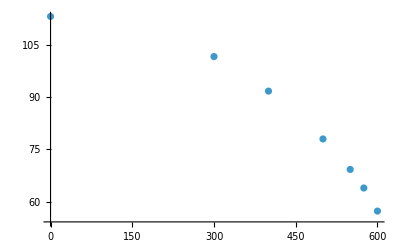

```mathematica
ListPlot[Transpose[{mub,T}]]
```

```mathematica
0.4*0.37
```

0.148